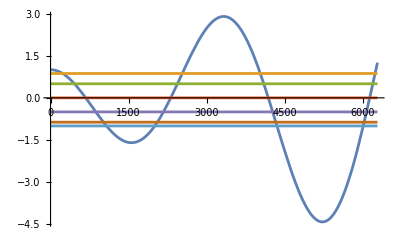

```mathematica
Plot[{Cos[Sqrt[0.000549/8.93]*x*0.2]-((0.116*x*10^-3)/(2*8.93))*Sqrt[8.93/0.000549]*Sin[Sqrt[0.000549/8.93]*x*0.2],Cos[Pi/6],Cos[Pi/3],Cos[Pi/2],Cos[2*Pi/3],Cos[5*Pi/6],Cos[Pi]},{x,0,2*Pi*1000}]
```

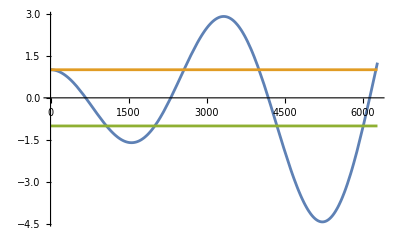

```mathematica
Plot[{Cos[Sqrt[0.000549/8.93]*x*0.2]-((0.116*x*10^-3)/(2*8.93))*Sqrt[8.93/0.000549]*Sin[Sqrt[0.000549/8.93]*x*0.2],1,-1},{x,0,2*Pi*1000}]
```

```mathematica
Sqrt(0.000549/8.93)
```

0.0000614782 Sqrt

```mathematica
Plot[Cos(Sqrt(0.000549/8.93)*x*0.2),{x,0,2*Pi})]
```

Syntax::bktmcp: 表达式 "Plot[Cos(Sqrt(0.000549/8.93)*x*0.2),{x,0,2*Pi}" 没有后面的 "]".

Syntax::sntxf: "(" 后面不能跟着 "Cos(Sqrt(0.000549/8.93)*x*0.2),{x,0,2*Pi})".

```mathematica
Plot[Cos(Sqrt(0.000549/8.93)*x*0.2),{x,0,2*Pi}]
```

-Graphics-

```mathematica
Cos[Sqrt[0.000549/8.93]*1*0.2]
```

0.999999

```mathematica
data={{260.476,261.776,262.086,262.186,262.246,262.275,262.355,262.356,262.362,262.378,262.389,262.402,262.413,262.428,262.438,262.450,262.466,262.479,262.490,262.502,262.511,262.531,262.546,262.565,262.586,262.616,262.686,262.746,262.846,262.926,263.167,264.747},{0.077,0.170,0.283,0.370,0.454,0.517,0.788,0.804,0.835,0.923,1.004,1.121,1.223,1.352,1.445,1.510,1.538,1.506,1.444,1.342,1.267,1.106,0.979,0.867,0.746,0.618,0.433,0.340,0.245,0.197,0.120,0.021}}//Transpose;
GraphicsGrid[{{ListCurvePathPlot[data,Epilog->{PointSize[0.008],Point[data]},PlotRange->All],ListLinePlot[data,Epilog->{PointSize[0.008],Point[data]},PlotRange->All]},{ListCurvePathPlot[data,Epilog->{PointSize[0.008],Point[data]},PlotRange->All,InterpolationOrder->2],ListLinePlot[data,Epilog->{PointSize[0.008],Point[data]},InterpolationOrder->2,PlotRange->All]}}]
```

-Graphics-

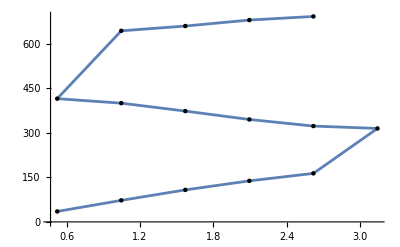

```mathematica
data={{Pi/6,Pi/3,Pi/2,2*Pi/3,5*Pi/6,Pi,5*Pi/6,2*Pi/3,Pi/2,Pi/3,Pi/6,Pi/3,Pi/2,2*Pi/3,5*Pi/6},{35.23,72.57,107.89,138.38,163.64,315.15,323.23,345.45,373.74,400.51,415.66,644.44,660.61,680.81,692.93}}//Transpose;
ListLinePlot[data,Epilog->{PointSize[0.008],Point[data]},PlotRange->All]
```

```mathematica
Plot
```